### Up until 1980 without blues

```mathematica
mins[assoc_]:=Keys[Select[assoc,#==Min[assoc]&]]
```

```mathematica
Module[{osc, firsts},osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&];firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];ListPlot[KeyValueMap[Callout[Style[{#2["Year"],#2["Period"]},PointSize[.01],Red],ArrayPlot[ArrayPad[#2["MatrixData"], 1],ImageSize->Tiny]]&,Select[osc, MemberQ[firsts, #Name]&]],PlotRange->{{1968,1980},{0,30}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Select[Lookup[osc,firsts], #Year<1981&]})]]
```

-Graphics-

### Up to present no blue

```mathematica
Module[{},osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&];firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];ListPlot[KeyValueMap[Callout[Style[{#2["Year"],#2["Period"]},PointSize[.01],Red],ArrayPlot[ArrayPad[#2["MatrixData"], 1],ImageSize->Tiny]]&,Select[osc, MemberQ[firsts, #Name]&]],PlotRange->{{1968,2025},{0,30}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Lookup[osc,firsts]})]]
```

-Graphics-

```mathematica
Module[{},osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&];firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];ListPlot[KeyValueMap[Callout[Style[{#2["Year"],#2["Period"]},PointSize[.01],Red],ArrayPlot[ArrayPad[#2["MatrixData"], 1],ImageSize->Tiny]]&,Select[osc, MemberQ[firsts, #Name]&]],PlotRange->{{1968,2025},{0,30}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Lookup[osc,firsts]})]]
```

### Size of pattern over year (with pad right)

```mathematica
all = Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime]
], {i,2 ,21}];
```

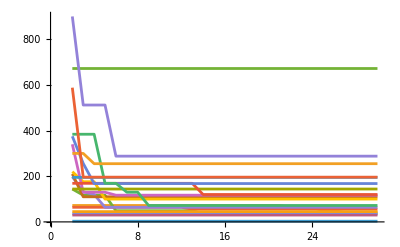

```mathematica
ListLinePlot[PadRight[#, 30, #[[-1]]]&/@all, PlotRange->{{0, 30}, All}]
```

```mathematica
Module[{},osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&];firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];ListPlot[KeyValueMap[Callout[Style[{#2["Year"],#2["Period"]},PointSize[.01],Red],ArrayPlot[ArrayPad[#2["MatrixData"], 1],ImageSize->Tiny]]&,Select[osc, MemberQ[firsts, #Name]&]],PlotRange->{{1968,2025},{0,30}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Lookup[osc,firsts]})]]
```

### Only improvements plots

```mathematica
ListPlot[Callout[Style[{#Year,#Period},PointSize[.01]],ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&/@ #&/@ Table[Module[{oscweightsovertime,improvements,locs,p=i},
weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]
], {i, 2, 22}], PlotStyle->RGBColor[0.23, 0.64, 1]]
```

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
firsts
```

{<|Name→Blinker,Period→2|>,<|Name→Cuphook,Period→3|>,<|Name→Pinwheel,Period→4|>,<|Name→Octagon 2,Period→5|>,<|Name→Sombreros,Period→6|>,<|Name→Airforce,Period→7|>,<|Name→Figure eight,Period→8|>,<|Name→Snacker,Period→9|>,<|Name→p10 traffic light hassler,Period→10|>,<|Name→38P11.1,Period→11|>,<|Name→Dinner table,Period→12|>,<|Name→Buckingham's p13,Period→13|>,<|Name→Tumbler,Period→14|>,<|Name→Pentadecathlon,Period→15|>,<|Name→Two pre-L hasslers,Period→16|>,<|Name→54P17.1,Period→17|>,<|Name→p18 bi-block hassler,Period→18|>,<|Name→Cribbage,Period→19|>,<|Name→145P20,Period→20|>,<|Name→124P21,Period→21|>,<|Name→168P22.1,Period→22|>}

```mathematica
Select[firsts, #Period == 22&]
```

{<|Name→168P22.1,Period→22,Year→1997|>}

```mathematica
firsts = Reap[points = Catenate[
Table[Module[{osc, weightsovertime,improvements,locs,p=i},
osc = SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
first = Sow[First[MinimalBy[osc, #Year&, 1]][[{"Name", "Period", "Year"}]]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@osc;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Callout[Style[{#Year,#Period}, If[#Name === first["Name"], Red, None]],ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&/@Reverse[osc[[locs]]]
], {i, 2, 22}]]][[2, 1]];ListPlot[points, Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@
firsts}), PlotRange->{{1969, 2025}, Automatic}]
```

-Graphics-

```mathematica
firsts = Reap[points = Catenate[
Table[Module[{osc, weightsovertime,improvements,locs,p=i},
osc = SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
first = Sow[First[MinimalBy[osc, #Year&, 1]][[{"Name", "Period", "Year"}]]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@osc;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Callout[Style[{#Year,#Period}, If[#Name === first["Name"], Red, None]],ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&/@Reverse[osc[[locs]]]
], {i, 2, 22}]]][[2, 1]];ListPlot[points, Epilog->({Opacity[.1],Table[Line[{{1969, i}, {2029, i}}], {i, 2, 26}]}), PlotRange->{{1969, 2025}, {2, 22}}, AspectRatio->.4, Frame->True, FrameLabel->{"year", "period"}]
```

-Graphics-

```mathematica
Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&]
```

```mathematica
osc[[1]]
```

```mathematica
Length[osc]
```

7

```mathematica
osc[[1]]
```

<|Name→168P22.1,Year→1997,Class→Oscillator,Period→22,Wiki→https://conwaylife.com/wiki/168P22.1,DataFiles→{168p22.1.cells,168p22.1.rle},MatrixData→SparseArray[Automatic,{23,33},0,{1,{{0,4,10,14,28,34,41,51,57,65,71,79,89,97,103,111,117,127,134,140,154,158,164,168},{{13},{14},{20},{21},{8},{9},{13},{21},{25},{26},{9},{14},{20},{25},{6},{7},{9},{11},{12},{13},{15},{19},{21},{22},{23},{25},{27},{28},{9},{11},{15},{19},{23},{25},{7},{9},{15},{17},{19},{25},{27},{8},{10},{13},{14},{16},{18},{20},{21},{24},{26},{9},{13},{16},{18},{21},{25},{5},{6},{15},{16},{18},{19},{28},{29},{1},{2},{5},{29},{32},{33},{1},{3},{5},{10},{24},{29},{31},{33},{3},{5},{6},{10},{11},{23},{24},{28},{29},{31},{1},{3},{5},{10},{24},{29},{31},{33},{1},{2},{5},{29},{32},{33},{5},{6},{15},{16},{18},{19},{28},{29},{9},{13},{16},{18},{21},{25},{8},{10},{13},{14},{16},{18},{20},{21},{24},{26},{7},{9},{15},{17},{19},{25},{27},{9},{11},{15},{19},{23},{25},{6},{7},{9},{11},{12},{13},{15},{19},{21},{22},{23},{25},{27},{28},{9},{14},{20},{25},{8},{9},{13},{21},{25},{26},{13},{14},{20},{21}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→168|>

### Multicolor

```mathematica
ListPlot[Callout[Style[{#Year,#Period},PointSize[.01]],ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&/@ #&/@ Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]
], {i, 2, 22}]]
```

-Graphics-

### Size instead of period

```mathematica
ListPlot[Callout[Style[{#Year,Times@@Dimensions[#MatrixData]},PointSize[.01]],ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&/@ #&/@ Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]
], {i, 2, 22}]]
```

-Graphics-

### Line plot?

```mathematica
ListLinePlot[Callout[Style[{#Year,Times@@Dimensions[#MatrixData]}],ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&/@ #&/@ Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]
], {i, 2, 22}], PlotStyle->PointSize[.015]]
```

-Graphics-

#### More periods

```mathematica
ListLinePlot[Callout[Style[{#Year,Times@@Dimensions[#MatrixData]}],ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&/@ #&/@ Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]
], {i, 2, 30}], PlotStyle->PointSize[.015], PlotRange->All]
```

-Graphics-

### Modularity over time

```mathematica
osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&];
```

```mathematica
aps = ParallelMap[PatternElements,SortBy[osc, #Year&][[All, "MatrixData"]]];
```

#### Part counts over time

```mathematica
Length[aps]
```

655

```mathematica
Length[SortBy[osc, #Year&][[All, "Year"]]]
```

655

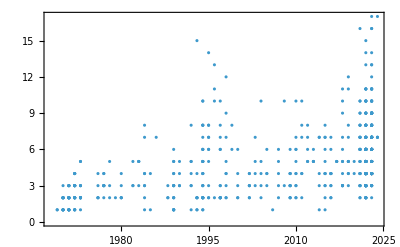

```mathematica
ListPlot[Transpose[Reverse@{Length[Keys[#]]&/@ Values[aps], Values[SortBy[osc, #Year&]][[All, "Year"]]}], Frame-> True, FrameLabel->{""}]
```

### Using morphological components

```mathematica
osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&];
```

```mathematica
aps = ParallelMap[MorphologicalComponents,SortBy[osc, #Year&][[All, "MatrixData"]]];
```

#### Part counts over time

```mathematica
Length[aps]
```

655

```mathematica
Length[SortBy[osc, #Year&][[All, "Year"]]]
```

655

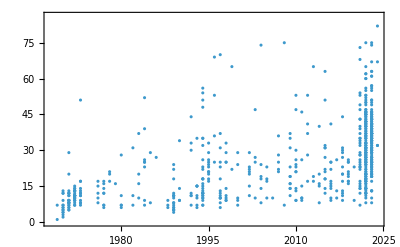

```mathematica
ListPlot[Transpose[Reverse@{Length/@ Values[aps], Values[SortBy[osc, #Year&]][[All, "Year"]]}], Frame-> True, FrameLabel->{""}]
```

#### With periods

Callouts not possible because there’s multiple parts

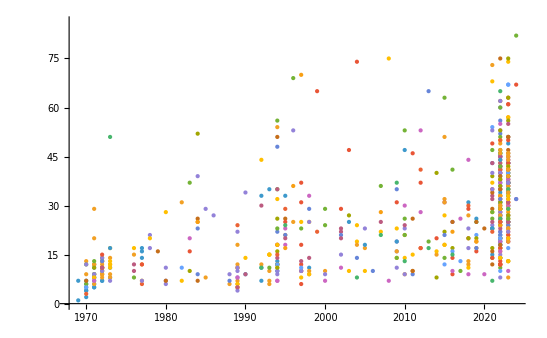

```mathematica
ListPlot[With[{pts = Transpose[Reverse@{Length/@ Values[aps], Values[SortBy[osc, #Year&]][[All, "Year"]]}]}, 
pts[[#]]&/@GatherBy[Range[Length[osc]], osc[[#, "Period"]]&]], PlotHighlighting->None]
```

### Highlighting a single dependency path over time (trying queen bee first)

```mathematica
$LifeParts[[1]]
```

$Aborted

```mathematica
all = Join[$LifeParts]
```

$Aborted

```mathematica
avs = Join@@Values[$LifeParts];
```

```mathematica
allpats = Catenate[avs];
```

```mathematica
Take[allpats, 1]
```

{{{1,1}}}

```mathematica
allpats[[1]]
```

{{1,1}}

```mathematica
avs[[1, 1]]
```

{{1,1}}

```mathematica
acs =Map[Count[avs, #]&,avs] ;
```

```mathematica
$LifeData["Herschel"]
```

<|Name→Herschel,Year→1970,Class→Methuselah,Wiki→https://conwaylife.com/wiki/Herschel,DataFiles→{herschel.cells,herschel.rle},MatrixData→SparseArray[Automatic,{4,3},0,{1,{{0,1,4,6,7},{{1},{1},{2},{3},{1},{3},{3}}},{1,1,1,1,1,1,1}}],InitialWeight→7|>